# Cálculo do fator de seguraça do revestimento ponto a ponto. Exemplo retirado de: (Rahman 1995)

## 1 - Tabela com propriedades dos tubos

```mathematica
(* 1 - Outside diameter(in) | 2 - Nominal weight(lb/ft) | 3 - Grade | 4 - Wall thickness (in) | 5 - Inside diameter (in) | 6 - Pipe collapse resistance (psi) | 7 - Body yield strength (1000 lbf) | 8 - Coupling type | 9 - Internal pressure resistance (psi) | 10 - Joint strength (1000 lbf) *)
```

```mathematica
PipesTable={
{20,       94,   K55,0.438,19.124,520,  1480,LTC,2110,955 },
{20,       133,K55,0.635,18.730,1500,2125,BTC,3036,2123},
{20,        65,   K55,0.375,15.250,630,  1012,STC,2260,625},
{16,        75,   K55,0.438,15.124,1020,1178,STC,2630,752},
{16,        84,   L80,0.495,15.010,1480,1929,BTC,4330,1861},
{16,        109, K55,0.656,14.688,2560,1739,BTC,3950,1895},
{13.375,98,  L80,0.719,11.937,5910,2800,BTC,7530,2286},
{13.375,85, P110,0.608,12.159,4690,2682,PTC,8750,2290},
{13.375,98, P110,0.719,11.937,7280,3145,PTC,10350,2800},
{9.625, 58.4,L80,0.595,8.435,7890,1350,BTC,8650,1396},
{9.625, 47,   P110,0.472,8.681,5310,1493,LTC,9449,1213},
{7,          38,V150,0.540,5.920,19240,1644,EXTL,18900,1430},
{7,          41,V150,0.590,5.820,22810,1782,PTC,20200,1052},
{7,          46,V150,0.670,5.660,25970,1999,PTC,25070,1344},
{7,          38,MW155,0.540,5.920,19700,1697,EXTL,20930,1592},
{7,          46,SOO140,0.670,5.660,24230,865,PTC,23400,1222},
{7,          46,SOO155,0.670,5.660,26830,2065,PTC,25910,1344}
};
```

## Métodos de interpolação

```mathematica
LinearEq[pt1_,pt2_]:=Block[{y,x,temp,temp2,temp3},
x=pt1[[1]]+(y-pt1[[2]])(pt2[[1]]-pt1[[1]])/(pt2[[2]]-pt1[[2]]);
Return[x]
]
```

```mathematica
Interpolate[ycoord_,data_]:=Block[{f,i,y},
For[i=1,i< Length[data],i++,
If[Abs[data[[i,2]]]≤Abs[ycoord]≤ Abs[data[[i+1,2]]],
f=LinearEq[data[[i]],data[[i+1]]];
Return[f/.y->ycoord];
];
];
];
```

## Janela operacional

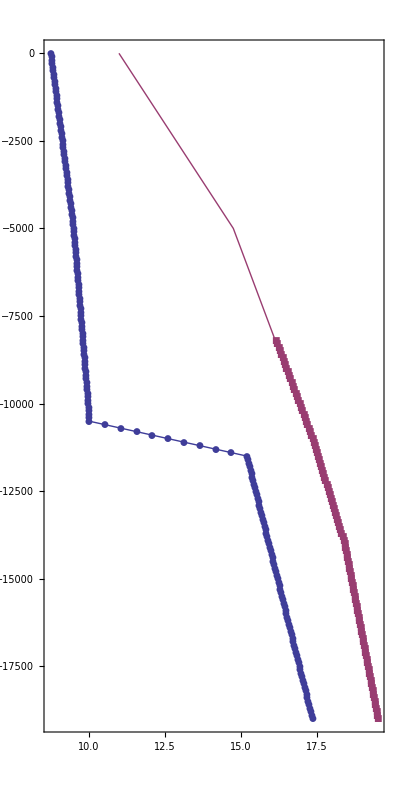

```mathematica
dataporepressure={{8.75,0},{9.5,-5000},{10.,-10250},{10,-10500},{15.2,-11500},{17.35,-19000}};
PtsFracPressure={{11,0},{14.76,-5000},{17.35,-11000},{18.4,-14000},{19.5,-19000}};
tabpore=Table[{Interpolate[y,dataporepressure],y},{y,-19000,0,100}];
tabfrac=Table[{Interpolate[y,PtsFracPressure],y},{y,-19000,0,100}];
ListLinePlot[{tabpore,tabfrac},AspectRatio->2,Frame->True,FrameLabel->{{" Depth (ft) "," "},{"Mud Density(ppg)","Operational Window"}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,Axes->None]
```

## Métodos de cálculo das pressões de ruptura, colapso e também do fator de segurança para o revestimento de superfície.

```mathematica
BurstSurface[h_,L_,datafracpressure_]:=Block[{PF,Psalt,Pgas,Pburst,eq1,eq2,sol,FracturePressure,hmud,hgas,rhogas=0.1/0.052,rhomud=12,rhosaltwater=0.465/0.052,rhofracatshoe,PI},
rhofracatshoe=Interpolate[-L,datafracpressure];
PI=0.052(rhofracatshoe+0.5) L;
Pgas=0.052rhogas (L-h);
Psalt=0.052rhosaltwater h;
Pburst=PI-Pgas-Psalt;
Pburst

];

ColapseSurface[h_,dataporepressure_]:=Block[{rhokick,PColapse},

rhokick=Interpolate[-h,dataporepressure];
PColapse=0.052rhokick h;
PColapse

];
```

```mathematica
ComputeSurfaceSafetyFactor[dataporepressure_,datafracpressure_,SurfaceData_,steps_]:=Block[{BurstPressure,ColapsePressure,tableburst={},tablecolapse={},L,h,sz,i,deltah,counter,BurstSF,ColapseSF,tableburstSF={},tablecolapseSF={}},

 sz=Length[SurfaceData];
L=SurfaceData[[sz,2]]-SurfaceData[[1,1]];
deltah=L/steps;
h=0;
counter=1;

For[i=1,i≤steps,i++,

BurstPressure=BurstSurface[h,L,datafracpressure];
ColapsePressure=ColapseSurface[h,dataporepressure];

BurstSF=SurfaceData[[counter,3]][[9]]/BurstPressure;
ColapseSF=SurfaceData[[counter,3]][[6]]/ColapsePressure;

AppendTo[tableburst,{BurstPressure,-h}];
AppendTo[tablecolapse,{ColapsePressure,-h}];
AppendTo[tableburstSF,{BurstSF,-h}];
AppendTo[tablecolapseSF,{ColapseSF,-h}];
h+=deltah;

If[h≥ SurfaceData[[counter,2]],
counter++;
];

];

{tableburst,tablecolapse,tableburstSF,tablecolapseSF}

]
```

```mathematica
SurfaceCasing={
{0.0001,3350.,PipesTable[[5]]},
{3550.,5000.,PipesTable[[6]]}
};
steps=100;
{listb,listc,listbsf,listcsf}=ComputeSurfaceSafetyFactor[dataporepressure,PtsFracPressure,SurfaceCasing,steps];
```

Power::infy: Infinite expression 1/0. encountered.

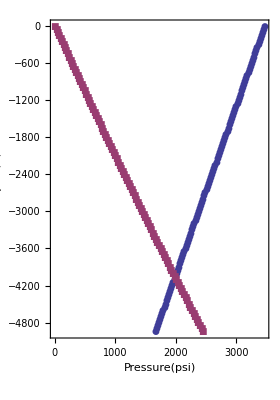

```mathematica
a=ListLinePlot[{listb,listc},AspectRatio->Automatic,Frame->True,FrameLabel->{{" Depth (ft) "," "},{"Pressure(psi)"," Surface Pressure: Burst(blue) vs colapse(red) "}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,PlotRange->{{0,5000},{0,-5000}}];
Show[a,PlotRange->All]
```

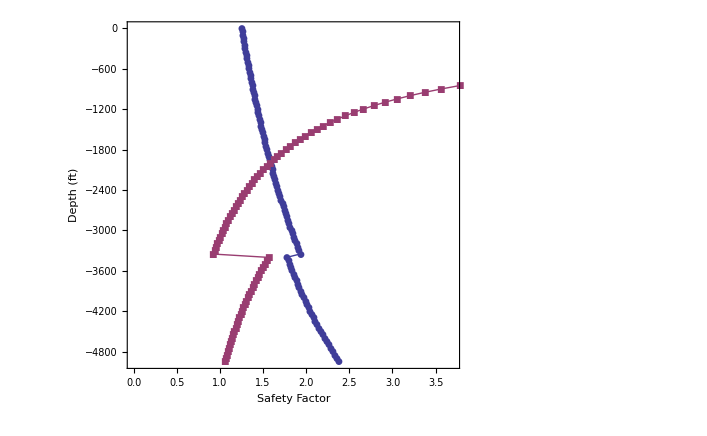

```mathematica
ListLinePlot[{listbsf,listcsf},Frame->True,FrameLabel->{{" Depth (ft) "," "},{" Safety Factor "," Surface Safety Factor: Burst(blue) vs colapse(red)"}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

## Métodos de cálculo das pressões de colapso, ruptura e também do fator de segurança para o revestimento intermediário.

```mathematica
ColapseIntermediate[h_,Lliner_,IntermediateData_, dataporepressure_]:=Block[{ha,hm1,hm2,ExtPress,InterPress,rhogas=0.1/0.052,rhomud=12,rhosaltwater=0.465/0.052,rhoheaviestmud=17.9,Linter,sz},
sz=Length[IntermediateData];
Linter=IntermediateData[[sz,2]];
hm2= rhosaltwater Lliner/rhoheaviestmud;
ha=Lliner-hm2;
hm1=Linter-ha;
If[h> ( Linter-hm1),
InterPress=0.052 rhoheaviestmud (h-(Linter-hm1));
ExtPress=0.052 rhomud h;
,
InterPress=0;
ExtPress=0.052 rhomud h;
];
ExtPress-InterPress
];
BurstIntermediate[h_,Lliner_,SurfacePressure_,IntermediateData_,datafracpressure_]:=Block[{rhofrac,rhogas=0.1/0.052,rhomud=12,rhosaltwater=0.465/0.052,rhoheaviestmud=17.9,eq1,eq2,InjectionPress,hmud,hgas,sol,InterPress,ExtPress,Linter,sz,hgi,Ptemp,lasth},
sz=Length[IntermediateData];
Linter=IntermediateData[[sz,2]];
rhofrac=Interpolate[-Lliner,datafracpressure];
InjectionPress=(rhofrac+0.5) 0.052 Lliner;
eq1=Lliner==hgas+hmud;
eq2=SurfacePressure==InjectionPress-0.052(rhogas hgas+rhoheaviestmud hmud);
sol=Solve[{eq1,eq2},{hmud,hgas}];
hmud=sol[[1,1,2]];
hgas=sol[[1,2,2]];
(*Print[hmud];
Print[hgas];*)
If[h≤ hmud,
(*Print["1"];*)
InterPress=SurfacePressure+0.052(rhoheaviestmud h);
ExtPress=0.052 rhosaltwater h;
,
(*Print["2"];*)
hgi=h-hmud;
Ptemp=SurfacePressure+0.052(rhoheaviestmud hmud);
InterPress=Ptemp+0.052(rhogas hgi);
ExtPress=0.052 rhosaltwater h;
];
(*Print["InterPress =",InterPress];
Print["ExtPress =",ExtPress];*)
InterPress-ExtPress
]
```

```mathematica
ComputeIntermediateSafetyFactor[dataporepressure_,datafracpressure_,IntermediateData_,Lliner_,SurfacePressure_,steps_]:=Block[{BurstPressure,ColapsePressure,tableburst={},tablecolapse={},L,h,sz,i,deltah,counter,BurstSF,ColapseSF,tableburstSF={},tablecolapseSF={}},

 sz=Length[IntermediateData];
L=IntermediateData[[sz,2]]-IntermediateData[[1,1]];
deltah=L/steps;
h=0;
counter=1;

For[i=1,i≤steps,i++,

BurstPressure=BurstIntermediate[h,Lliner,SurfacePressure,IntermediateData,datafracpressure];
ColapsePressure=ColapseIntermediate[h,Lliner,IntermediateData, dataporepressure];
BurstSF=IntermediateData[[counter,3]][[9]]/BurstPressure;
ColapseSF=IntermediateData[[counter,3]][[6]]/ColapsePressure;

AppendTo[tableburst,{BurstPressure,-h}];
AppendTo[tablecolapse,{ColapsePressure,-h}];
AppendTo[tableburstSF,{BurstSF,-h}];
AppendTo[tablecolapseSF,{ColapseSF,-h}];
h+=deltah;

If[h≥ IntermediateData[[counter,2]],
counter++;
];

];

{tableburst,tablecolapse,tableburstSF,tablecolapseSF}

]
```

```mathematica
IntermediateCasing={
{0.0001,4000.,PipesTable[[7]]},
{4000,6400,PipesTable[[8]]},
{6400,11100,PipesTable[[9]]}
};
Lliner=14000;
SurfacePressure=5000;
steps=100;
{listb,listc,listbsf,listcsf}=ComputeIntermediateSafetyFactor[dataporepressure,PtsFracPressure,IntermediateCasing,Lliner,SurfacePressure,steps];
```

Power::infy: Infinite expression 1/0. encountered.

```mathematica
BurstIntermediate[11100,14000,5000,IntermediateCasing,PtsFracPressure]
BurstIntermediate[8859,14000,5000,IntermediateCasing,PtsFracPressure]
```

8307.7

9125.66

```mathematica
ColapseIntermediate[11100,14000,IntermediateCasing, dataporepressure]
ColapseIntermediate[7006,14000,IntermediateCasing, dataporepressure]
```

3115.72

4371.74

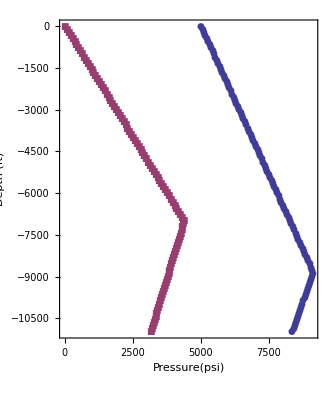

```mathematica
ListLinePlot[{listb,listc},AspectRatio->Automatic,Frame->True,FrameLabel->{{" Depth (ft) "," "},{"Pressure(psi)"," Intermediate Pressure: Burst(blue) vs colapse(red) "}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic]
```

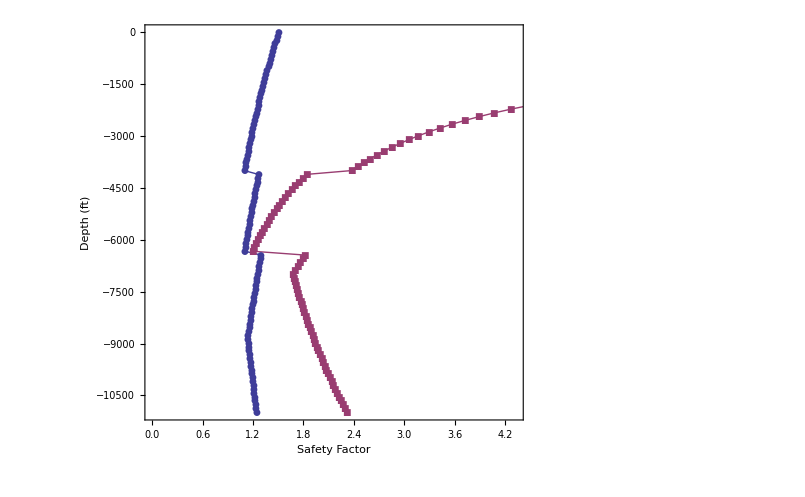

```mathematica
ListLinePlot[{listbsf,listcsf},Frame->True,FrameLabel->{{" Depth (ft) "," "},{" Safety Factor "," Intermediate Safety Factor: Burst(blue) vs colapse(red)"}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

## Métodos de cálculo das pressões de colapso, ruptura e também do fator de segurança para o liner.

```mathematica
ColapseLiner[h_,LinerData_, dataporepressure_]:=Block[{ExterPress,InternPress,rhomud=12,rhoheaviestmud=17.9,rhosaltwater=0.465/0.052,hm2,ha,sz,Lliner},
sz=Length[LinerData];
Lliner=LinerData[[sz,2]];
hm2= rhosaltwater Lliner/rhoheaviestmud;
ha=Lliner-hm2;
ExterPress=0.052rhomud h;
InternPress=0.052 rhoheaviestmud(h-ha);
ExterPress-InternPress
]
BurstLiner[h_,LinerData_,SurfacePressure_,datafracpressure_]:=Block[{rhofrac,rhogas=0.1/0.052,rhomud=12,rhosaltwater=0.465/0.052,rhoheaviestmud=17.9,eq1,eq2,InjectionPress,hmud,hgas,sol,InterPress,ExtPress,Linter,sz,hgi,Ptemp,lasth,Lliner,InternPress,ExterPress},
sz=Length[LinerData];
Lliner=LinerData[[sz,2]];
rhofrac=Interpolate[-Lliner,datafracpressure];
InjectionPress=(rhofrac+0.5) 0.052 Lliner;
eq1=Lliner==hgas+hmud;
eq2=SurfacePressure==InjectionPress-0.052(rhogas hgas+rhoheaviestmud hmud);
sol=Solve[{eq1,eq2},{hmud,hgas}];
hmud=sol[[1,1,2]];
hgas=sol[[1,2,2]];
InternPress=SurfacePressure+hmud rhoheaviestmud 0.052+(h-hmud)rhogas 0.052;
ExterPress=0.052rhosaltwater h;
InternPress-ExterPress
]
```

```mathematica
ComputeLinerSafetyFactor[dataporepressure_,datafracpressure_,LinerData_,SurfacePressure_,steps_]:=Block[{BurstPressure,ColapsePressure,tableburst={},tablecolapse={},L,h,sz,i,deltah,counter,BurstSF,ColapseSF,tableburstSF={},tablecolapseSF={}},

 sz=Length[LinerData];
L=LinerData[[sz,2]]-LinerData[[1,1]];
deltah=L/steps;
h=LinerData[[1,1]];
counter=1;

For[i=1,i≤steps,i++,

BurstPressure=BurstLiner[h,LinerData,SurfacePressure,datafracpressure];
ColapsePressure=ColapseLiner[h,LinerData, dataporepressure];
BurstSF=LinerData[[counter,3]][[9]]/BurstPressure;
ColapseSF=LinerData[[counter,3]][[6]]/ColapsePressure;

AppendTo[tableburst,{BurstPressure,-h}];
AppendTo[tablecolapse,{ColapsePressure,-h}];
AppendTo[tableburstSF,{BurstSF,-h}];
AppendTo[tablecolapseSF,{ColapseSF,-h}];
h+=deltah;

If[h≥ LinerData[[counter,2]],
counter++;
];

];

{tableburst,tablecolapse,tableburstSF,tablecolapseSF}

]
```

```mathematica
LinerData={
{10500,12500,PipesTable[[10]]},
{12500,14000,PipesTable[[9]]}
};
SurfacePressure=5000;
steps=50;
{listb,listc,listbsf,listcsf}=ComputeLinerSafetyFactor[dataporepressure,PtsFracPressure,LinerData,SurfacePressure,steps];
```

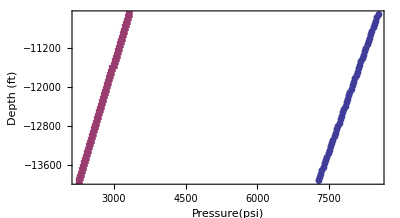

```mathematica
ListLinePlot[{listb,listc},AspectRatio->Automatic,Frame->True,FrameLabel->{{" Depth (ft) "," "},{"Pressure(psi)"," Liner Pressure: Burst(blue) vs colapse(red) "}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,Axes->None]
```

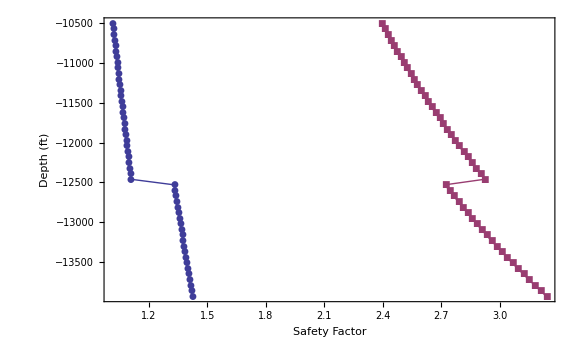

```mathematica
ListLinePlot[{listbsf,listcsf},Frame->True,FrameLabel->{{" Depth (ft) "," "},{" Safety Factor "," Liner Safety Factor: Burst(blue) vs colapse(red)"}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic]
```

```mathematica
PipesTable[[9]]
```

{13.375,98,P110,0.719,11.937,7280,3145,PTC,10350,2800}

```mathematica
PipesTable[[10]]
```

{9.625,58.4,L80,0.595,8.435,7890,1350,BTC,8650,1396}

## Métodos de cálculo das pressões de colapso, ruptura e também do fator de segurança para o revestimento de produção.

```mathematica
ColapseProduction[h_,ProductionData_]:=Block[{ExterPress,InternPress,rhoheaviestmud=17.9},
ExterPress=0.052rhoheaviestmud (14000/19000)h;
InternPress=0;
ExterPress-InternPress
]
BurstProduction[h_,ProductionData_,SurfacePressure_,dataporepressure_]:=Block[{rhogas=0.1/0.052,rhomud=12,rhosaltwater=0.465/0.052,rhoheaviestmud=17.9,rhoformation,Ltotal,sz,InternPress,ExternPress},

sz=Length[ProductionData];
Ltotal=ProductionData[[sz,2]];
rhoformation=Interpolate[-Ltotal,dataporepressure];
InternPress=(rhoformation  Ltotal-rhogas Ltotal)0.052+(rhoheaviestmud h)0.052;
ExternPress=rhosaltwater h 0.052;
InternPress-ExternPress

]
```

```mathematica
ComputeProductionSafetyFactor[dataporepressure_,datafracpressure_,ProductionData_,SurfacePressure_,steps_]:=Block[{BurstPressure,ColapsePressure,tableburst={},tablecolapse={},L,h,sz,i,deltah,counter,BurstSF,ColapseSF,tableburstSF={},tablecolapseSF={}},

 sz=Length[ProductionData];
L=ProductionData[[sz,2]]-ProductionData[[1,1]];
deltah=L/steps;
h=0;
counter=1;

For[i=1,i≤steps,i++,

BurstPressure=BurstProduction[h,ProductionData,SurfacePressure,dataporepressure];
ColapsePressure=ColapseProduction[h,ProductionData];
BurstSF=ProductionData[[counter,3]][[9]]/BurstPressure;
ColapseSF=ProductionData[[counter,3]][[6]]/ColapsePressure;

AppendTo[tableburst,{BurstPressure,-h}];
AppendTo[tablecolapse,{ColapsePressure,-h}];
AppendTo[tableburstSF,{BurstSF,-h}];
AppendTo[tablecolapseSF,{ColapseSF,-h}];
h+=deltah;

If[h≥ ProductionData[[counter,2]],
counter++;
];

];

{tableburst,tablecolapse,tableburstSF,tablecolapseSF}

]
```

```mathematica
ColapseProduction[19000,ProductionData]
BurstProduction[19000,ProductionData,SurfacePressure,dataporepressure]
```

13031.2

Part::partd: Part specification ProductionData ⟦ 0, 2 ⟧ is longer than depth of object.

8850.2+0.052 (-1.92308 ProductionData⟦0,2⟧+Null ProductionData⟦0,2⟧)

```mathematica
ProductionData={
{0,3000,PipesTable[[12]]},
{3000,8000,PipesTable[[15]]},
{8000,16000,PipesTable[[14]]},
{16000,19000,PipesTable[[17]]}
};
SurfacePressure=5000;
steps=50;
{listb,listc,listbsf,listcsf}=ComputeProductionSafetyFactor[dataporepressure,PtsFracPressure,ProductionData,SurfacePressure,steps];
```

Power::infy: Infinite expression 1/0. encountered.

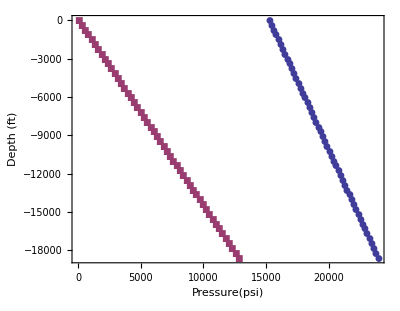

```mathematica
ListLinePlot[{listb,listc},AspectRatio->Automatic,Frame->True,FrameLabel->{{" Depth (ft) "," "},{"Pressure(psi)"," Production Pressure: Burst(blue) vs colapse(red) "}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic]
```

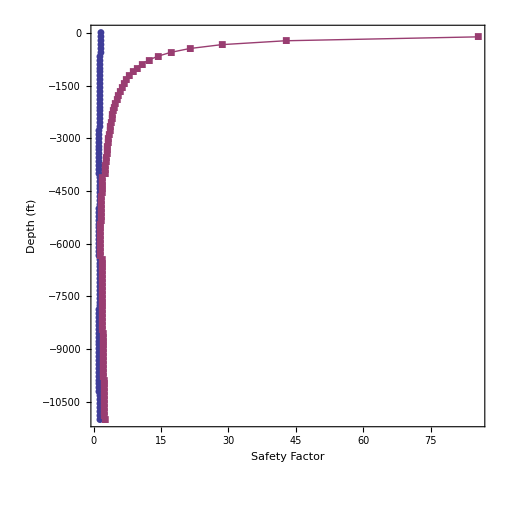

```mathematica
ListLinePlot[{listbsf,listcsf},Frame->True,FrameLabel->{{" Depth (ft) "," "},{" Safety Factor "," Production Safety Factor: Burst(blue) vs colapse(red)"}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,PlotRange->{{0,5},{0,-19000}},AspectRatio->1]
```